```mathematica
({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}})ᵀ.({{λ1, 0}, {0, λ2}}).({{Cos[θ], -Sin[θ]}, {Sin[θ], Cos[θ]}})
```

{{λ1 Cos[θ]^2+λ2 Sin[θ]^2,-λ1 Cos[θ] Sin[θ]+λ2 Cos[θ] Sin[θ]},{-λ1 Cos[θ] Sin[θ]+λ2 Cos[θ] Sin[θ],λ2 Cos[θ]^2+λ1 Sin[θ]^2}}

```mathematica
FullSimplify[Eigensystem[{{λ1 Cos[θ]^2+λ2 Sin[θ]^2,-λ1 Cos[θ] Sin[θ]+λ2 Cos[θ] Sin[θ]},{-λ1 Cos[θ] Sin[θ]+λ2 Cos[θ] Sin[θ],λ2 Cos[θ]^2+λ1 Sin[θ]^2}}],{λ1>λ2}]
```

{{λ1,λ2},{{-Cot[θ],1},{Tan[θ],1}}}

```mathematica
FullSimplify[-λ1 Cos[θ] Sin[θ]+λ2 Cos[θ] Sin[θ]]
```

(-λ1+λ2) Cos[θ] Sin[θ]

```mathematica
sols=FullSimplify[Solve[
{t11==λ1 Cos[θ]^2+λ2 Sin[θ]^2,
t12==-λ1 Cos[θ] Sin[θ]+λ2 Cos[θ] Sin[θ],
t22==λ2 Cos[θ]^2+λ1 Sin[θ]^2}
,{λ1,λ2,θ}]⟦2⟧/. C[1]->0,Assumptions->t11>t22]
```

{λ1→1/2 (t11+√(4 t12^2+(t11-t22)^2)+t22),λ2→1/2 (t11-√(4 t12^2+(t11-t22)^2)+t22),θ→ArcTan[2 √((t11+√(4 t12^2+(t11-t22)^2)-t22)/(√(4 t12^2+(t11-t22)^2))),-(4 t12)/(√(4 t12^2+(t11-t22)^2) √((t11+√(4 t12^2+(t11-t22)^2)-t22)/(√(4 t12^2+(t11-t22)^2))))]}

```mathematica
FullSimplify[{Cos[θ],-Sin[θ]}/.sols⟦2⟧,Assumptions->{t11>t22,t12∈Reals}]
```

{(√(t11+√(4 t12^2+(t11-t22)^2)-t22))/(√2 (4 t12^2+(t11-t22)^2)^(1/4)),(√2 t12)/((4 t12^2+(t11-t22)^2)^(1/4) √(t11+√(4 t12^2+(t11-t22)^2)-t22))}

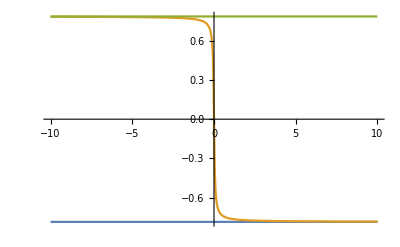

```mathematica
Block[{t11=1,t22=0.9},
Plot[{-π/4,θ/.sols⟦2⟧,π/4},{t12,-10,10}]
]
```

```mathematica
Ψ[x,y]:=1/2 T11 x^2+T12 x y + 1/2 T22 y^2+1/(3!)(T111 x^3+3 T112 x^2 y+3 T122 x y^2+T222 y^3)
```

```mathematica
D[Ψ[x,y],x,x]/.{x->0,y->0}
D[Ψ[x,y],x,y]/.{x->0,y->0}
D[Ψ[x,y],y,y]/.{x->0,y->0}

D[Ψ[x,y],x,x,x]/.{x->0,y->0}
D[Ψ[x,y],x,x,y]/.{x->0,y->0}
D[Ψ[x,y],x,y,y]/.{x->0,y->0}
D[Ψ[x,y],y,y,y]/.{x->0,y->0}
```

T11

T12

T22

T111

T112

T122

T222

```mathematica
eigen=FullSimplify[Eigenvalues[D[D[Ψ[x,y],{{x,y}}],{{x,y}}]],T11>T22]
```

{1/2 (T11+T22+T111 x+T122 x+T112 y+T222 y-√((T11+T22+(T111+T122) x+(T112+T222) y)^2-4 (-T12^2+T11 T22+x (T11 T122-T112^2 x+T111 (T22+T122 x))+T222 (T11+T111 x) y+T112 (T22-T122 x) y+(-T122^2+T112 T222) y^2-2 T12 (T112 x+T122 y)))),1/2 (T11+T22+T111 x+T122 x+T112 y+T222 y+√((T11+T22+(T111+T122) x+(T112+T222) y)^2-4 (-T12^2+T11 T22+x (T11 T122-T112^2 x+T111 (T22+T122 x))+T222 (T11+T111 x) y+T112 (T22-T122 x) y+(-T122^2+T112 T222) y^2-2 T12 (T112 x+T122 y))))}

```mathematica
FullSimplify[eigen/.{x->0,y->0},T11>T22]
```

{1/2 (T11-√(4 T12^2+(T11-T22)^2)+T22),1/2 (T11+√(4 T12^2+(T11-T22)^2)+T22)}

```mathematica
FullSimplify[D[eigen⟦2⟧,{{x,y}}]/.{x->0,y->0},Assumptions->{T11>T22,T12∈Reals}]
```

{1/2 (T111+T122+(4 T112 T12+(T111-T122) (T11-T22))/(√(4 T12^2+(T11-T22)^2))),1/2 (T112+(4 T12 T122+(T11-T22) (T112-T222))/(√(4 T12^2+(T11-T22)^2))+T222)}